```mathematica
Clear["Global`*"];
```

```mathematica
Off[N::preclg];
Off[NIntegrate::ncvb];
Off[NIntegrate::slwcon];
```

```mathematica
Sech2Imp[T0_,CalcWindow_,N0_]:=Table[N[Sech[t/T0]],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
Gauss2Imp[T0_,CalcWindow_,N0_]:=Table[N[Exp[-(t^2(2 √(2Log[2]))^2)/(2 T0^2)]],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
Box2Imp[T0_,CalcWindow_,N0_]:=Table[N[UnitBox[t/T0]],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
SechAmp2Imp[Energy_,T0_,CalcWindow_,N0_]:=Sech2Imp[T0,CalcWindow,N0]×√(Energy/NIntegrate[Interpolation[Transpose[{Table[t,{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}],Sech2Imp[T0, CalcWindow, N0]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}]);
GaussAmp2Imp[Energy_,T0_,CalcWindow_,N0_]:=Gauss2Imp[T0,CalcWindow,N0]×√(Energy/NIntegrate[Interpolation[Transpose[{Table[t,{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}],Gauss2Imp[T0, CalcWindow, N0]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}]);
BoxAmp2Imp[Energy_,T0_,CalcWindow_,N0_]:=Box2Imp[T0,CalcWindow,N0]×√(Energy/NIntegrate[Interpolation[Transpose[{Table[t,{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}],Box2Imp[T0, CalcWindow, N0]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}]);
```

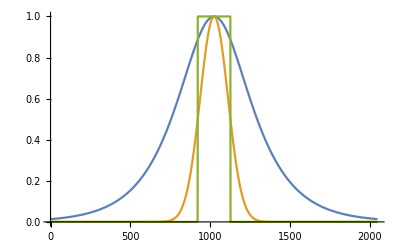
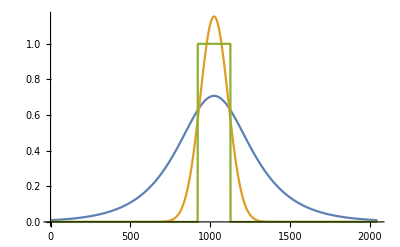

```mathematica
{ListPlot[{Sech2Imp[1,5,2047],Gauss2Imp[1,5,2047],Box2Imp[1,5,2047]},PlotRange->All,Joined->True],
ListPlot[{SechAmp2Imp[1,1,5,2047],GaussAmp2Imp[1,1,5,2047],BoxAmp2Imp[1,1,5,2047]},PlotRange->All,Joined->True]}
```

```mathematica
Frequency2Wavelength[λ0_,CalcWindow_,N0_]:=(LightSpeed=3×10^5;Return[Table[N[10^6 10^3(2 π LightSpeed)/(Δω+(2 π LightSpeed)/(λ0×10^-6×10^-3))], {Δω, -π/(CalcWindow×10^-12)×(N0-1)/2,π/(CalcWindow×10^-12)×(N0-1)/2,π/(CalcWindow×10^-12)}]]);
Frequency2DeltaWavelength[λ0_,CalcWindow_,N0_]:=(LightSpeed=3×10^5;Return[Table[N[10^6 10^3(λ0×10^-6×Δω)/(LightSpeed/(λ0×10^-6)-Δω)], {Δω, -π/(CalcWindow×10^-12)×(N0-1)/2,π/(CalcWindow×10^-12)×(N0-1)/2,π/(CalcWindow×10^-12)}]]);
```

```mathematica
FrequencyTable[CalcWindow_,N0_]:=RotateLeft[Table[π/CalcWindow×i, {i, -(N0-1)/2,(N0-1)/2,1}],(N0-1)/2];
DispersionTable[CalcWindow_,N0_]:=RotateLeft[Table[(π/CalcWindow×i)^2, {i, -(N0-1)/2,(N0-1)/2,1}],(N0-1)/2];
Dispersion[β2_, CalcWindow_,N0_, h_]:=Exp[(I β2 h)/2 ×DispersionTable[CalcWindow,N0]];
Loss[α_,h_]:=Exp[-α/2×h];
Spatial[γ_,h_,x_]:=Exp[I γ h ×Abs[x]^2];
```

```mathematica
SSFT[CalcWindow_,h_,L_,β2_,γ_,α_,A0_]:=
Monitor[(
ξ="Starting";
N0=Length[A0];
Aω=Fourier[A0]×1/(√Dispersion[β2,CalcWindow,N0,h]);
At=InverseFourier[Aω];
At*=Loss[α,h/2];
ξ=0;
For[ξ=h/2,ξ<L,ξ+=h,
Aω=Fourier[At];
Aω*=Dispersion[β2,CalcWindow,N0,h];
At=InverseFourier[Aω];
At*=Spatial[γ,h,At];
At*=Loss[α,h];
];
ξ="Finishing";
Aω=Fourier[At];
Aω*=√Dispersion[β2,CalcWindow,N0,h];
At = InverseFourier[Aω];
At*=Loss[α,h/2];
Return[At];
)
,If[NumberQ[ξ],0×ξ+Round[(ξ×100)/L],ξ]]
```

```mathematica
MyDifferences[x_List]:=Table[If[i==1,x[[i+1]]-x[[i]],If[i==Length[x],-x[[i-1]]+x[[i]],(x[[i+1]]-x[[i-1]])/2]],{i,Length[x]}];
InstantFrequency[x_List]:=-MyDifferences[x];
```

```mathematica
CutInstantFrequency[x_List]:=Select[x,Abs[#[[2]]]<1&];
GetIntegratePhaseFromInstantFrequency[x_List]:=Transpose[{x[[All,1]],Accumulate[x[[All,2]]]}];
```

```mathematica
GetOutput[A0_List,At_List,WavelengthArray_List,TimeArray_List] := (
N0=Length[A0];
PulseIn=Transpose[{TimeArray,Abs[A0]^2}];
PulseOut=Transpose[{TimeArray,Abs[At]^2}];
SpectrumIn=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[A0]]^2,(N0-1)/2]}];
SpectrumOut=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[At]]^2,(N0-1)/2]}];
InstantFrequencyIn=CutInstantFrequency[Transpose[{TimeArray,InstantFrequency[Arg[A0]]}]];
InstantFrequencyOut=CutInstantFrequency[Transpose[{TimeArray,InstantFrequency[Arg[At]]}]];
PhaseIn=GetIntegratePhaseFromInstantFrequency[InstantFrequencyIn];
PhaseOut=GetIntegratePhaseFromInstantFrequency[InstantFrequencyOut];
N0=Length[A0];
{ListPlot[{PulseIn,PulseOut},PlotRange->All,Joined->True,ImageSize->Medium,PlotLabel->"Входной и выходной импульсы"],
ListPlot[{SpectrumIn,SpectrumOut},PlotRange->{{1.3,1.9},Full},Joined->True,ImageSize->Medium,PlotLabel->"Входной и выходной спектры"],
ListPlot[{PhaseIn,PhaseOut},PlotRange->All,Joined->True,ImageSize->Medium,PlotLabel->"Фаза"],ListPlot[{InstantFrequencyIn,InstantFrequencyOut},PlotRange->All,Joined->True,ImageSize->Medium,PlotLabel->"Мгновенная частота"]}
);
```

```mathematica
CalcWindow=20.0; (* пс, ширина окна расчёта *)
T0=1.0; (* ширина импульса *)
N0=2^11-1; (* временная дискретизация *)
h=0.0002; (* км, пространственная дискретизация *)
N0=N0-Boole[EvenQ[N0]]; (* чтобы число расчётных точек было всё равно нечётным, вне зависимости от того, какой был начальный N0 *)
L=0.2; (* км, длина пролёта *)
β2=-22.0×1; (* пс^2/км, дисперсия групповых скоростей *)
γ=1.25×0; (* 1/(Вт × км), фазовая самомодуляция *)
α=-0.2×10^3×0; (* 1/км, поглощение или усиление *)
λ0=1.55; (* мкм, длина волны *)
WavelengthArray = Frequency2Wavelength[λ0,CalcWindow,N0];
TimeArray=Table[N[t],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
```

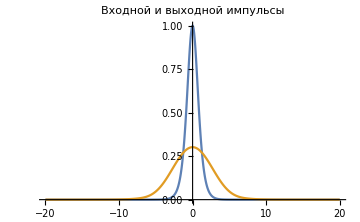
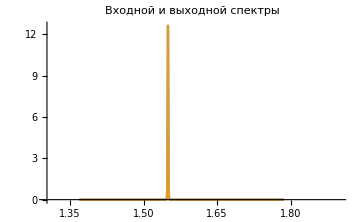
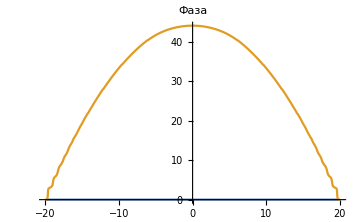
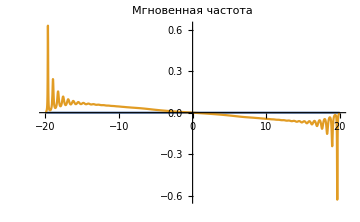

```mathematica
A0=Sech2Imp[T0,CalcWindow,N0];
At=SSFT[CalcWindow,h,L,β2,γ,α,A0];
GetOutput[A0,At,WavelengthArray,TimeArray]
```

```mathematica
Abs[At[[(N0-1)/2]]]^2/Abs[A0[[(N0-1)/2]]]^2
```

0.301811

```mathematica
ListLogPlot[RotateLeft[Abs[Fourier[At]]^2,(Length[At]-1)/2],PlotRange->All];
```

```mathematica
Gauss[σ_,ω0_,ω_]:=1/(σ √(2π))Exp[-(ω-ω0)^2/(2 σ^2)];
GaussianFrequencyFilter[A_List,FrequencyArray_List,σ_,ω0_]:=InverseFourier[Fourier[A]×Gauss[σ,ω0,FrequencyArray]];
```

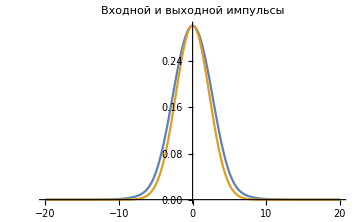
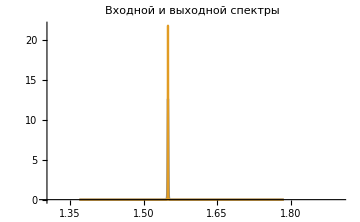
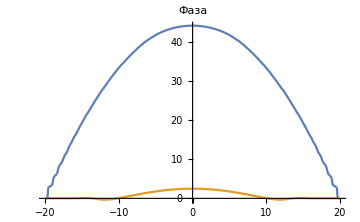
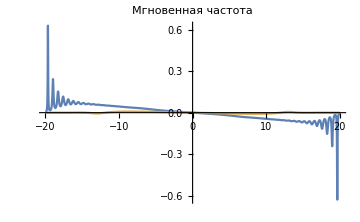

```mathematica
Δλ=1;
σ = Δλ/(2 √(2Log[2]));
AFiltered = GaussianFrequencyFilter[At,FrequencyTable[CalcWindow,N0],σ,0];
GetOutput[At,Abs[At[[(N0+1)/2]]]/Abs[AFiltered[[(N0+1)/2]]]×AFiltered,WavelengthArray,TimeArray]
```

```mathematica
CalcWindow=10; (* пс, ширина окна расчёта *)
T0=1.0; (* ширина импульса *)
Energy=12; (* пДж, энергия в импульсе *)
N0=2^12-1; (* временная дискретизация *)
h=0.0000005; (* км, пространственная дискретизация *)
L=0.006; (* км, длина пролёта *)
β2=25.×1; (* пс^2/км, дисперсия групповых скоростей *)
γ=5.8×1; (* 1/(Вт × км), фазовая самомодуляция*)
α=-1.9×10^3×1; (* 1/км, поглощение или усиление *)
λ0=1.55; (* км, длина волны *)
TimeArray=Table[N[t],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
WavelengthArray=Frequency2Wavelength[λ0,CalcWindow,N0];
A0=GaussAmp2Imp[Energy,T0,CalcWindow,N0];
```

```mathematica
At=SSFT[CalcWindow,h,L,β2,γ ,α,A0];
GetOutput[A0,1×At,WavelengthArray,TimeArray]
{EnergyIn=NIntegrate[Interpolation[Transpose[{TimeArray,Abs[A0]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}],
EnergyOut=NIntegrate[Interpolation[Transpose[{TimeArray,Abs[At]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}],
EnergyOut/EnergyIn}
```

{12.,1.07288×10^6,89406.6}

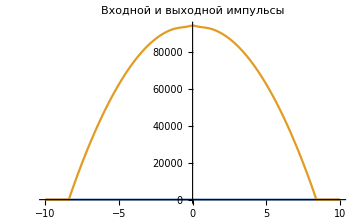
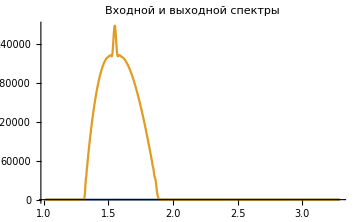
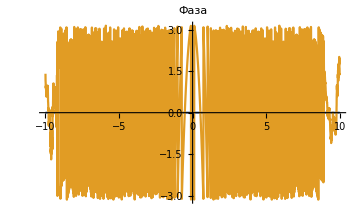
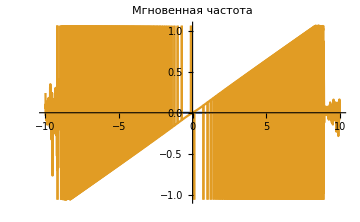
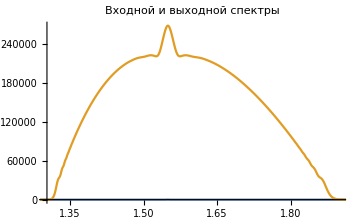
CalcWindow=10; h=0.0000005; N0=2^12-1;
{EnergyIn=12.,EnergyOut=1.07288×10^6,EnergyIn/EnergyOut=89406.6}
Симиляритон - это когда и усиление, и дисперсия, и ФСМ. Импульс похож на параболу. Аттрактор
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CalcWindow=10; (* пс, ширина окна расчёта *)
T0=1.0; (* ширина импульса *)
Energy=12; (* пДж, энергия в импульсе *)
N0=2^12-1; (* временная дискретизация *)
h=0.00000005; (* км, пространственная дискретизация *)
L=0.003; (* км, длина пролёта *)
β2=25.×1; (* пс^2/км, дисперсия групповых скоростей *)
γ=5.8×1; (* 1/(Вт × км), фазовая самомодуляция*)
α=-1.9×10^3×1; (* 1/км, поглощение или усиление *)
λ0=1.55; (* км, длина волны *)
TimeArray=Table[N[t],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
WavelengthArray=Frequency2Wavelength[λ0,CalcWindow,N0];
A0=BoxAmp2Imp[Energy,T0,CalcWindow,N0];
```

```mathematica
At=SSFT[CalcWindow,h,L,β2,γ ,α,A0];
GetOutput[A0,1×At,WavelengthArray,TimeArray]
{EnergyIn=NIntegrate[Interpolation[Transpose[{TimeArray,Abs[A0]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}],
EnergyOut=NIntegrate[Interpolation[Transpose[{TimeArray,Abs[At]^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}],
EnergyOut/EnergyIn}
```

Запись полученных результатов